```mathematica
(*Matrix size and block size*)
n=12000;  (*Total dimension*)
blockSize=10;  (*Size of each block*)

(*Generate block-diagonal Hermitian matrix*)
H=BlockDiagonalMatrix[Table[RandomVariate[GaussianOrthogonalMatrixDistribution[blockSize]],Ceiling[n/blockSize]]];

(*Compute eigenvalues*)
eigenvalues=Sort@Eigenvalues[H];
```

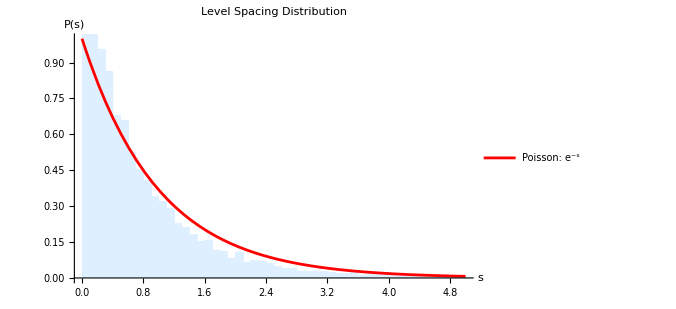

```mathematica
(*Compute unfolded level spacings*)
spacings=Differences[eigenvalues];
spacings=spacings/Mean[spacings]; (*Unfolding*)

(*Plot level-spacing distribution*)
Show[Histogram[spacings,{0.1},"PDF",PlotRange->{{0,5},{0,1}},ChartStyle->LightBlue,PlotLabel->"Level Spacing Distribution"],Plot[Exp[-s],{s,0,5},PlotStyle->Red,PlotLegends->{"Poisson: \!\(\*SuperscriptBox[\(e\), \(-s\)]\)"}],AxesLabel->{"s","P(s)"},ImageSize->500]
```